Raman Sideband Cooling Simulation

## 0. Configuration

Simulation Parameters

```mathematica
nmax = 15;
```

Physical System

```mathematica
(*Branching Factor*)
α = 0.6;
(*Transition wavelength*)
λ = 670.992 10^-9 ;
(*Lattice Wavelength*)
λLat = 532 10^-9;
(*Intensity of lattice beam*)
IntensityLat = 1 /(10^-4);
(*Excited State Decay Width*)
Γ = 1/(27.102 10^-9);
(*Lattice Spacing*)
ω0 = 2 Pi 1.3 10^6;
(*Lamb Dicke Parameter*)
η = 0.25;

(*Raman*)
λRm1 = λ;
λRm2 = λ;
IntRm1 = 0.0000001 * 227 10^4;
IntRm2 = 0.0000001 * 20 10^4;
ΩRm1 = Sqrt[(Ωfree 2 Δ12 9 hbar Δ32)/(2 Sqrt[2] EFS Sin[Φ])](*Sqrt[(3 λRm1^3 Γ IntRm1)/(2 Pi h c)]*)
ΩRm2 = Sqrt[(Ωfree 2 Δ12 9 hbar Δ32)/(2 Sqrt[2] EFS Sin[Φ])] (*Sqrt[(3 λRm2^3 Γ IntRm2)/(2 Pi h c)]*)
EFS = 2 Pi 10 10^9 hbar;
Δ12 = 5/(2 Pi) 10^9;
Δ32 =  5 /(2 Pi)10^9;
Φ = 135/180 Pi;
Ωfree = 30 2 Pi 10^3 //N(*(ΩRm1 ΩRm2)/(2 Δ12) (2 Sqrt[2])/9 EFS/(hbar Δ32) Sin[Φ]*)
ΔRm = 7.3 10^9;
(*Repump*)
Int = 0.6 10^-3/(10^-4); (*Repump Intensity*)
ΔR = 4 10^6;
(*lattice params*)
LatticeScatteringPrefactor = 1.00217872738179 10^-9 ;
a = 1.15 10^-6;
σ = 0.1 *3 * (265 10^-12)^2/(2 Pi);
ρ = 1/a^2;
RCs = 200;
δ1 =  1;
δ2 = 1;
Ω1 =  η Ωfree; (*actually imaginary*)
mCs = 132.90545 * 1.660539 10^-27 ;
```

4.13497×10^6

4.13497×10^6

188496.

Physical Constants and auxiliary methods

```mathematica
c = 2.997 10^8;hbar = 1.0545718×10^-34;
ω = c 2 Pi/λ;
ωLat = c * 2 Pi / (λLat);
kb = 1.38066 10^-23;
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
Ωn = Ω1 Sqrt[n];
h = 2 Pi *hbar;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)]
```

1.26809×10^7

6.9115

## 1. Extract Scattering Rates from 3-level Master Equation

Set::write: Tag Plus in +{-8276.1} is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Plus in +{-8276.1} is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Plus in +{-8276.1} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

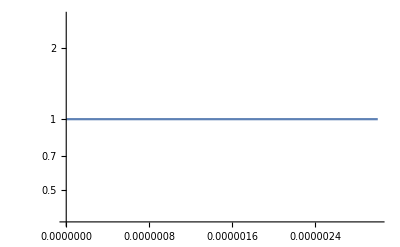
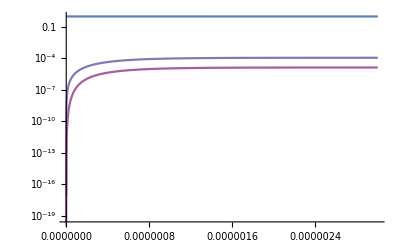
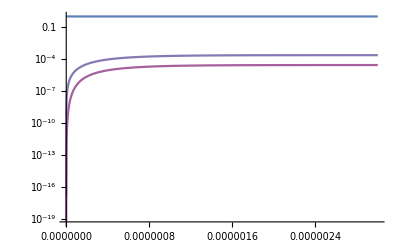
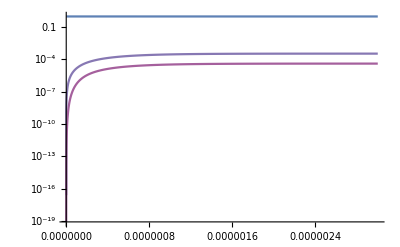
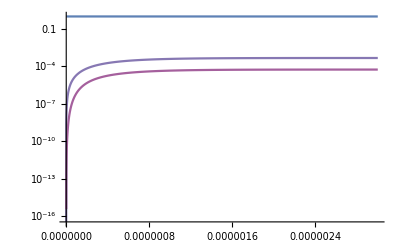
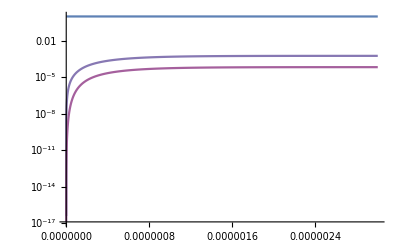
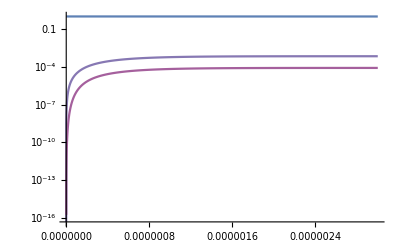
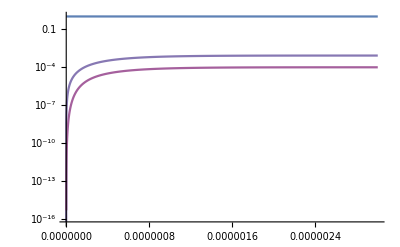
{{0,0,-Graphics-},{1,-9458.4,-Graphics-},{2,-10186.,-Graphics-},{3,-11034.8,-Graphics-},{4,-12038.,-Graphics-},{5,-13241.8,-Graphics-},{6,-14713.1,-Graphics-},{7,-16552.2,-Graphics-},{8,-18916.8,-Graphics-},{9,-22069.6,-Graphics-},{10,-26483.5,-Graphics-},{11,-33104.4,-Graphics-},{12,-44139.2,-Graphics-},{13,-66208.8,-Graphics-},{14,-132418.,-Graphics-},{15,ComplexInfinity,-Graphics-},{16,132418.,-Graphics-}}

{0,-9458.4,-10186.,-11034.8,-12038.,-13241.8,-14713.1,-16552.2,-18916.8,-22069.6,-26483.5,-33104.4,-44139.2,-66208.8,-132418.,ComplexInfinity,132418.}

```mathematica
Clear[P1list,P2list,P3list];
P1list = {};
P2list = {};
P3list = {};
tab = Table[
(*alpha factor to be guessed /measured*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2 = ρ22 /. First[sol];
expsol = Solve[Re[fun3[4 10^-4  ]] == Re[fun3[1 10^-4 ]] Exp[-l 3 10^-4 ],l]; +
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];

AppendTo[P1list, Re[fun1[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P2list, Re[fun2[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P3list, Re[fun3[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];

{n,lam, LogPlot[Evaluate[ρe[t]/.sol],{t,0,3*10*10^-7} , PlotRange -> All, PlotRange -> {Automatic, {10^-7,1}}]}
(*LogPlot[Evaluate[ρe[t]/.sol],{t,0,3*10*10^-5} , PlotRange -> All, PlotRange -> {Automatic, {10^-7,1}}]*)
,{n,0,16}]
Γscatt = tab[[All, 2]]
```

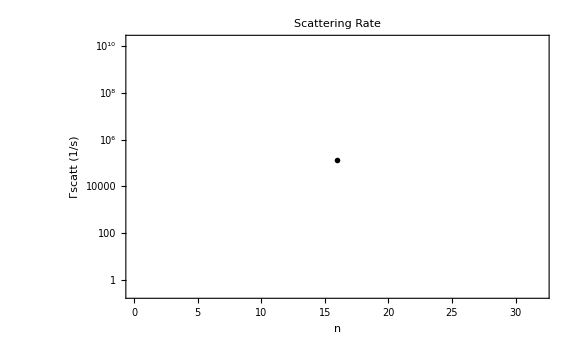

```mathematica
ListLogPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True, Joined -> True, PlotMarkers->{Automatic, Small}, PlotStyle-> Black, FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}]
```

## 2. Calculating Heating and Cooling Rates

```mathematica
Photon recoil
```

```mathematica
Γscatt;
pphoton = h / λ;
Erecoil = pphoton^2/(2mCs); (*has to be corrected actually!!!*)

Λreca= Γscatt * Erecoil;
Λrece= Γscatt * Erecoil;
Λrecarate= Γscatt * Erecoil    2/(3 kb) *10^3;
Λrecerate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,0.943813,1.87766,2.80192,3.71702,4.62307,5.52187,6.41015,7.29831,8.17364,9.03974,9.90264,10.759,11.6089,12.4534,ComplexInfinity}

```mathematica
Off-resonant scattering: Raman
```

```mathematica
Ephoton = h * c/λ;
ΛscRm =Table[ Γ    (ΩRm1^2 + ΩRm2^2)/(4 ΔRm^2) Erecoil ,{n,0,15}] 2/(3 kb)10^3
```

{0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805,0.00989805}

```mathematica
Off-resonant scattering: Repump beam
```

```mathematica
ΛscRp = P1list* Γ ΩR^2/(4 ΔR^2)Erecoil 2/(3 kb)10^3
```

{9890.01,9866.54,9843.31,9820.31,9797.53,9774.96,9752.57,9730.36,9708.32,9686.43,9664.68,9643.06,9621.56,9600.18,9578.9,9557.72}

```mathematica
Lattice beams
```

```mathematica
(*ephoton not precise, should be average over all resonances*)
(*numerical value taken from last weeks simulartion*)
```

```mathematica
ΛscLat =  Table[LatticeScatteringPrefactor* IntensityLat Erecoil 2/(3 kb) *10^3 ,{n,0,15}] (*probably neglegible*)
```

{1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9,1.06911×10^-9}

```mathematica
Off-Res Raman Couplings: Carrier transitions n-> n
```

```mathematica
Ωcarrier = Table[Ω1 (1-0.5 η^2(2n+1)),{n,0,15}];
Λcarrier = Table[P1list[[n+1]] ΩR^2/Γ Ωcarrier[[n+1]]^2/(4 ω0^2),{n,0,15}]2*Erecoil 2/(3 kb) *10^3
```

{1.7841,1.55761,1.347,1.15214,0.972907,0.809194,0.660884,0.527869,0.410039,0.307291,0.219519,0.146622,0.0884995,0.0450525,0.0161829,0.00179413}

```mathematica
Off-Res Raman Couplings: Blue transitions
```

```mathematica
Ωblue = Table[Ω1 (Sqrt[n+1]),{n,0,15}]//N;

Λblue= Table[P1list[[n+1]] ΩR^2/Γ Ωblue[[n+1]]^2/(16 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{92.6509,184.862,276.64,367.992,458.923,549.439,639.544,729.242,818.539,907.437,995.94,1084.05,1171.77,1259.1,1346.05,1432.61}

```mathematica
Off-Res Raman Couplings: Doubly red
```

```mathematica
Ωdoublyred= Table[Ωcarrier[[1]]*η^2*Sqrt[(n-1)*n],{n,0,15}]//N;

Λdoublyred = -Table[P1list[[n+1]] ΩR^2/Γ Ωdoublyred[[n+1]]^2/(4 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{0.,0.,-2.70438,-8.09418,-16.1508,-26.856,-40.1917,-56.1403,-74.6841,-95.806,-119.489,-145.715,-174.468,-205.731,-239.488,-275.721}

```mathematica
Rescattering
```

```mathematica
Λresc = Table[(P1list[[n+1]]α+P2list[[n+1]](1-α)) 1.00217872738179 10^9 (σ ρ)/2 Log[RCs],{n,0,15}]*2/(3 kb) *10^3 *2* Erecoil
```

{0.00143614,0.00143274,0.00142936,0.00142602,0.00142272,0.00141944,0.00141619,0.00141296,0.00140976,0.00140658,0.00140342,0.00140028,0.00139716,0.00139406,0.00139097,0.00138789}

```mathematica
Repumping of state 2
```

```mathematica
Γ2s = ΩR^2 Γ/(Γ^2+4 δ2^2);
ΛRepump = Table[P2list[[n+1]] * Γ2s *2* Erecoil,{n,0,15}] 2/(3 kb) *10^3
```

{0.,1.89487,3.76991,5.62634,7.46533,9.28805,11.0956,12.889,14.6693,16.4375,18.1945,19.9412,21.6783,23.4066,25.127,26.8399}

```mathematica
Cooling Rate
```

```mathematica
Λcool = -Table[P3list[[n+1]] α Abs[Dr[n-1,n-1]]^2*Γ,{n,0,15}] 2/(3 kb) *10^3 hbar ω0;
Λcool[[1]] = 0;
Λcool
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{0,-345.69,-604.449,-789.257,-911.723,-982.203,-1009.91,-1003.02,-968.735,-913.425,-842.652,-761.27,-673.486,-582.923,-492.672,-405.348}

```mathematica
Generate table
```

```mathematica
TableOfValues2=MapThread[Prepend,{{{"n = 0","n=1","n=2","n=3","n=4","n=5","n=6","n=7","n=8","n=9","n=10"},Λrecarate, Λrecerate,Λcarrier ,Λblue  ,ΛscRm ,ΛscRp ,Λresc,ΛscLat, Λdoublyred,Λcool},{"μK/ms","Λrecarate", "Λrecerate","Λcarrier" ,"Λblue"  ,"ΛscRm" ,"ΛscRp" ,"Λresc","ΛscLat","Λdoublyred","Λcool"}}];
Grid[TableOfValues2[[All,{1,2,3,6,8,10,12}]],ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True},Background->{None,{{LightOrange,LightGray}}}]
```

μK/ms | n = 0 | n=1 | n=4 | n=6 | n=8 | n=10
Λrecarate | 0. | 0.943813 | 3.71702 | 5.52187 | 7.29831 | 9.03974
Λrecerate | 0. | 0.943813 | 3.71702 | 5.52187 | 7.29831 | 9.03974
Λcarrier | 1.7841 | 1.55761 | 0.972907 | 0.660884 | 0.410039 | 0.219519
Λblue | 92.6509 | 184.862 | 458.923 | 639.544 | 818.539 | 995.94
ΛscRm | 0.00989805 | 0.00989805 | 0.00989805 | 0.00989805 | 0.00989805 | 0.00989805
ΛscRp | 9890.01 | 9866.54 | 9797.53 | 9752.57 | 9708.32 | 9664.68
Λresc | 0.00143614 | 0.00143274 | 0.00142272 | 0.00141619 | 0.00140976 | 0.00140342
ΛscLat | 1.06911×10^-9 | 1.06911×10^-9 | 1.06911×10^-9 | 1.06911×10^-9 | 1.06911×10^-9 | 1.06911×10^-9
Λdoublyred | 0. | 0. | -16.1508 | -40.1917 | -74.6841 | -119.489
Λcool | 0 | -345.69 | -911.723 | -1009.91 | -968.735 | -842.652

## 3. Matrix Elements (from seperate notebook)

```mathematica
Matrix Elements (from seperate notebook)
```

```mathematica
Matd ={{1.5337604188090186+0. ⅈ,0.11966389269178948+0. ⅈ,0.01156800726156411+0. ⅈ,0.001411048591966118+0. ⅈ,0.00021468875392546886+0. ⅈ,0.00003846590032110959+0. ⅈ,7.807444535791458*^-6+0. ⅈ,1.752707152273474*^-6+0. ⅈ,4.2781137299856986*^-7+0. ⅈ,1.1209643791990949*^-7+0. ⅈ,3.1223296738263093*^-8+0. ⅈ,9.17405856060743*^-9+0. ⅈ,2.8254571391355983*^-9+0. ⅈ,9.063420222659191*^-10+0. ⅈ,2.9795875404897314*^-10+0. ⅈ,9.98857424257307*^-11+0. ⅈ},{0.11966389269178945+0. ⅈ,1.317568647948566+0. ⅈ,0.19728890211322309+0. ⅈ,0.02709648524859807+0. ⅈ,0.004119013838066189+0. ⅈ,0.0007356294336309946+0. ⅈ,0.00014937501756307666+0. ⅈ,0.00003353670260266542+0. ⅈ,8.185543191506932*^-6+0. ⅈ,2.144799442424796*^-6+0. ⅈ,5.974130813190523*^-7+0. ⅈ,1.755324238013795*^-7+0. ⅈ,5.40610523196523*^-8+0. ⅈ,1.7341549846251833*^-8+0. ⅈ,5.701011876762306*^-9+0. ⅈ,1.91116989427912*^-9+0. ⅈ},{0.011568007261564112+0. ⅈ,0.19728890211322322+0. ⅈ,1.1551404700774563+0. ⅈ,0.24927288605279438+0. ⅈ,0.04356765819011158+0. ⅈ,0.007783908963170216+0. ⅈ,0.0015734879499190568+0. ⅈ,0.0003534581650443352+0. ⅈ,0.0000862856998746892+0. ⅈ,0.000022607566015886554+0. ⅈ,6.297096093130969*^-6+0. ⅈ,1.85022663363369*^-6+0. ⅈ,5.698386802326275*^-7+0. ⅈ,1.8279115840044158*^-7+0. ⅈ,6.009235940075373*^-8+0. ⅈ,2.01449696284489*^-8+0. ⅈ},{0.0014110485919661187+0. ⅈ,0.02709648524859808+0. ⅈ,0.2492728860527945+0. ⅈ,1.028984433463344+0. ⅈ,0.28450080953013546+0. ⅈ,0.059701502001262+0. ⅈ,0.012097002433284385+0. ⅈ,0.002701015397591902+0. ⅈ,0.0006597779765406222+0. ⅈ,0.00017291557893999224+0. ⅈ,0.000048159929335859994+0. ⅈ,0.000014150323113285317+0. ⅈ,4.3580951170707355*^-6+0. ⅈ,1.3979765171531368*^-6+0. ⅈ,4.595826661544421*^-7+0. ⅈ,1.5406750506838148*^-7+0. ⅈ},{0.00021468875392546886+0. ⅈ,0.004119013838066189+0. ⅈ,0.04356765819011159+0. ⅈ,0.28450080953013546+0. ⅈ,0.928685162557259+0. ⅈ,0.30823208183895656+0. ⅈ,0.07495341033531347+0. ⅈ,0.01682218579234278+0. ⅈ,0.004076931631546757+0. ⅈ,0.0010691978594604377+0. ⅈ,0.00029791975835811996+0. ⅈ,0.00008752511407614463+0. ⅈ,0.000026955923255357564+0. ⅈ,8.64694464071561*^-6+0. ⅈ,2.842671030081411*^-6+0. ⅈ,9.529573379349921*^-7+0. ⅈ},{0.000038465900321109594+0. ⅈ,0.000735629433630995+0. ⅈ,0.007783908963170215+0. ⅈ,0.059701502001261994+0. ⅈ,0.3082320818389565+0. ⅈ,0.8475752206230598+0. ⅈ,0.3237892281011723+0. ⅈ,0.08911042981100728+0. ⅈ,0.021789140423117807+0. ⅈ,0.005657588272601433+0. ⅈ,0.0015774155924708098+0. ⅈ,0.0004637270344278081+0. ⅈ,0.00014279856828211822+0. ⅈ,0.00004580527740505525+0. ⅈ,0.000015058693809651374+0. ⅈ,5.048180033411273*^-6+0. ⅈ},{7.807444535791461*^-6+0. ⅈ,0.00014937501756307674+0. ⅈ,0.001573487949919057+0. ⅈ,0.012097002433284385+0. ⅈ,0.0749534103353135+0. ⅈ,0.3237892281011725+0. ⅈ,0.7811464707560863+0. ⅈ,0.33338084531452916+0. ⅈ,0.10211370537428019+0. ⅈ,0.026878287380940908+0. ⅈ,0.007402187503414653+0. ⅈ,0.0021771337418679563+0. ⅈ,0.0006710462735876647+0. ⅈ,0.00021521500142190764+0. ⅈ,0.00007074810600626288+0. ⅈ,0.000023717744775128895+0. ⅈ},{1.7527071522734678*^-6+0. ⅈ,0.00003353670260266529+0. ⅈ,0.0003534581650443339+0. ⅈ,0.002701015397591892+0. ⅈ,0.016822185792342723+0. ⅈ,0.089110429811007+0. ⅈ,0.3333808453145265+0. ⅈ,0.7262158098272709+0. ⅈ,0.3385373835587837+0. ⅈ,0.11397570994644733+0. ⅈ,0.03200704994925855+0. ⅈ,0.00927470132716163+0. ⅈ,0.002859180131807137+0. ⅈ,0.000918171364983374+0. ⅈ,0.00030177832369475486+0. ⅈ,0.0001011579210327856+0. ⅈ},{4.278113729983148*^-7+0. ⅈ,8.185543191502053*^-6+0. ⅈ,0.00008628569987463771+0. ⅈ,0.0006597779765402284+0. ⅈ,0.004076931631544328+0. ⅈ,0.021789140423104984+0. ⅈ,0.10211370537421564+0. ⅈ,0.3385373835585461+0. ⅈ,0.6804546454268016+0. ⅈ,0.3403570125912493+0. ⅈ,0.12474014931464827+0. ⅈ,0.03711876564169128+0. ⅈ,0.011243051013147945+0. ⅈ,0.003609227723067272+0. ⅈ,0.0011883209035745655+0. ⅈ,0.00039825800456630965+0. ⅈ},{1.120964379234697*^-7+0. ⅈ,2.1447994424929174*^-6+0. ⅈ,0.00002260756601660457+0. ⅈ,0.000172915578945483+0. ⅈ,0.0010691978594944236+0. ⅈ,0.005657588272781529+0. ⅈ,0.02687828738177181+0. ⅈ,0.11397570995016162+0. ⅈ,0.34035701260873874+0. ⅈ,0.6421081777559666+0. ⅈ,0.33965105849336+0. ⅈ,0.13446087741391782+0. ⅈ,0.04217008287886575+0. ⅈ,0.01326391011603635+0. ⅈ,0.004361997966833031+0. ⅈ,0.0014651675316673044+0. ⅈ},{3.122329675986239*^-8+0. ⅈ,5.97413081732325*^-7+0. ⅈ,6.297096097487105*^-6+0. ⅈ,0.000048159929369172634+0. ⅈ,0.00029791975856427385+0. ⅈ,0.0015774155935634271+0. ⅈ,0.007402187508477785+0. ⅈ,0.03200704997149804+0. ⅈ,0.12474014941796335+0. ⅈ,0.3396510585601643+0. ⅈ,0.6098187799161146+0. ⅈ,0.33702900086964144+0. ⅈ,0.14317654986475595+0. ⅈ,0.04707371964892928+0. ⅈ,0.015126255653191152+0. ⅈ,0.005070508818816466+0. ⅈ},{9.174057921928472*^-9+0. ⅈ,1.7553241158117873*^-7+0. ⅈ,1.8502265048249378*^-6+0. ⅈ,0.000014150322128155827+0. ⅈ,0.00008752510798286732+0. ⅈ,0.0004637270021552676+0. ⅈ,0.0021771335901127928+0. ⅈ,0.009274700679088385+0. ⅈ,0.03711876313733161+0. ⅈ,0.13446086808844626+0. ⅈ,0.33702895733111793+0. ⅈ,0.5824957164328187+0. ⅈ,0.33290562230056575+0. ⅈ,0.15074114864366317+0. ⅈ,0.05119512480852333+0. ⅈ,0.01672187286026799+0. ⅈ},{2.825456475273183*^-9+0. ⅈ,5.406103961760106*^-8+0. ⅈ,5.698385463442789*^-7+0. ⅈ,4.358094093116586*^-6+0. ⅈ,0.000026955916922223944+0. ⅈ,0.00014279853471204797+0. ⅈ,0.0006710461159768814+0. ⅈ,0.002859179467065056+0. ⅈ,0.011243048285669788+0. ⅈ,0.04217007180790023+0. ⅈ,0.14317654919757994+0. ⅈ,0.3329053066608716+0. ⅈ,0.55907209674702+0. ⅈ,0.32716812281399343+0. ⅈ,0.15522945513986833+0. ⅈ,0.05409734531798155+0. ⅈ},{9.064423695639196*^-10+0. ⅈ,1.7343469847463798*^-8+0. ⅈ,1.8281139645402593*^-7+0. ⅈ,1.398131296335814*^-6+0. ⅈ,8.647902011455644*^-6+0. ⅈ,0.00004581034894537425+0. ⅈ,0.00021523882240935977+0. ⅈ,0.000918273052875275+0. ⅈ,0.0036096291691487177+0. ⅈ,0.013265355749100894+0. ⅈ,0.047078733140624704+0. ⅈ,0.15076313287588824+0. ⅈ,0.3271890722929206+0. ⅈ,0.5361782226800967+0. ⅈ,0.3151592705658968+0. ⅈ,0.15628111089847924+0. ⅈ},{2.971474821167179*^-10+0. ⅈ,5.685489356284483*^-9+0. ⅈ,5.992874197975165*^-8+0. ⅈ,4.583313294560272*^-7+0. ⅈ,2.8349311114019883*^-6+0. ⅈ,0.000015017692964316283+0. ⅈ,0.00007055546347695963+0. ⅈ,0.00030095660815248286+0. ⅈ,0.001185089539389658+0. ⅈ,0.004350096666569633+0. ⅈ,0.015084465392968276+0. ⅈ,0.05106265546864549+0. ⅈ,0.15487028036173794+0. ⅈ,0.3127411811338504+0. ⅈ,0.48953250536674353+0. ⅈ,0.3201766640445192+0. ⅈ},{1.0059323284565803*^-10+0. ⅈ,1.9247067044268376*^-9+0. ⅈ,2.0287656389157223*^-8+0. ⅈ,1.551587663614428*^-7+0. ⅈ,9.59707092004951*^-7+0. ⅈ,5.083935576613545*^-6+0. ⅈ,0.000023885771379760085+0. ⅈ,0.00010187430587434378+0. ⅈ,0.0004010695174030868+0. ⅈ,0.0014756523895217467+0. ⅈ,0.005107431178096411+0. ⅈ,0.01681750814919589+0. ⅈ,0.05446740212850906+0. ⅈ,0.16019427500990222+0. ⅈ,0.30446625806509053+0. ⅈ,0.26713032520432095+0. ⅈ}};
```

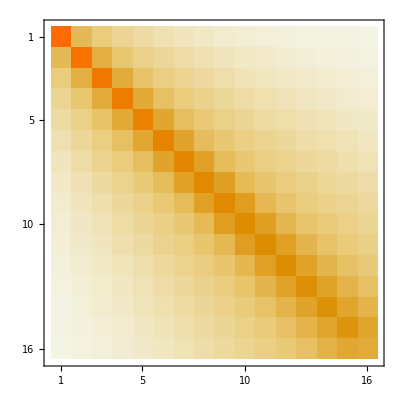

```mathematica
MatrixPlot[Matd,FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}]
```

## 4. Dressed State Rate Equation

```mathematica
Γeff[n_]:=Γscatt[[n]]
Γheatpre = Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]]),{n,0,15}] 
Γheat = Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]])α/(3 Erecoil)(2/(3 kb) *10^3)^-1,{n,0,15}] (*cheated*)
```

Infinity::indet: Indeterminate expression 10714.6+ComplexInfinity+ComplexInfinity encountered.

{9984.46,10054.9,10122.4,10187.,10248.7,10307.6,10363.6,10416.8,10467.2,10514.7,10559.4,10601.4,10640.5,10676.8,10710.4,Indeterminate}

Infinity::indet: Indeterminate expression 10714.6+ComplexInfinity+ComplexInfinity encountered.

{3.11979×10^7,3.14179×10^7,3.16288×10^7,3.18307×10^7,3.20237×10^7,3.22077×10^7,3.23827×10^7,3.25489×10^7,3.27063×10^7,3.28548×10^7,3.29945×10^7,3.31255×10^7,3.32478×10^7,3.33613×10^7,3.34662×10^7,Indeterminate}

```mathematica
Pm[t_]:= {P0[t],P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]};
Pmen = {P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15};
```

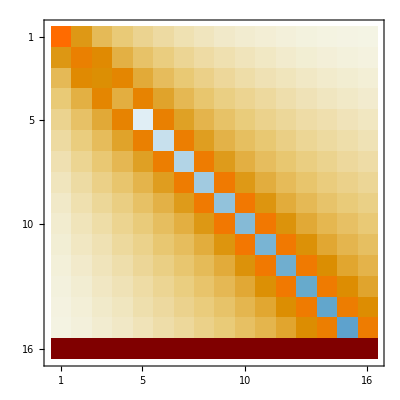

```mathematica
(*Clear[Γeff, Matd, Γheat, α]*)
R = Table[+α(Γeff[n+1]*Matd[[n+1,nt]]+Γheat[[n+1]]*Matd[[n+1,nt+1]]), {n,0,nmax},{nt,0,nmax}] ;
For[i=1,i≤ nmax+1,i++,R[[i,i]] = R[[i,i]] -(Γeff[i]+ Γheat[[i]])];
For[i=1,i≤ nmax+1,i++,R[[i,1]] = α Γheat[[i]]*Matd[[i,1]]];
R[[1,1]] =-(Γeff[1]+ Γheat[[1]]) +  α Γheat[[1]]*Matd[[1,1]];
R //MatrixForm;
MatrixPlot[R, FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}]
```

```mathematica
system = Pm'[t] == R.Pm[t] ;
init=Pm[0]=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{P0[0],P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0],P11[0],P12[0],P13[0],P14[0],P15[0]}=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=NDSolve[LogicalExpand[Pm'[t]==R.Pm[t]&&init],Pmen,{t,0,0.01}]
LogLogPlot[Evaluate[{P0[t], P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]}/.sol],{t,0,0.0002}, PlotRange -> All, Frame-> True, FrameLabel->{{"Time"},{"Population Pn"}},FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}, PlotLegends -> Table[n,{n,1,16}]]
```

LogicalExpand::elist: List encountered during logical expansion of {ρ11[0]==1,ρ12[0]==0,ρ13[0]==0,ρ21[0]==0,ρ22[0]==0,ρ23[0]==0,ρ31[0]==0,ρ32[0]==0,ρ33[0]==0}.

NDSolve::deqn: Equation or list of equations expected instead of … in the first argument ….

NDSolve[LogicalExpand[{P0'[t],P1'[t],P2'[t],P3'[t],P4'[t],P5'[t],P6'[t],P7'[t],P8'[t],P9'[t],P10'[t],P11'[t],P12'[t],P13'[t],P14'[t],P15'[t]}=={(1.66522×10^7+0. ⅈ) P0[t]+(3.73326×10^6+0. ⅈ) P1[t]+(0.974102+0. ⅈ) P10[t]+(0.286212+0. ⅈ) P11[t]+(0.0881484+0. ⅈ) P12[t]+(0.028276+0. ⅈ) P13[t]+(0.00929569+0. ⅈ) P14[t]+(0.00311623+0. ⅈ) P15[t]+(360898.+0. ⅈ) P2[t]+(44021.8+0. ⅈ) P3[t]+(6697.84+0. ⅈ) P4[t]+(1200.06+0. ⅈ) P5[t]+(243.576+0. ⅈ) P6[t]+(54.6808+0. ⅈ) P7[t]+(13.3468+0. ⅈ) P8[t]+(3.49718+0. ⅈ) P9[t],(3.75959×10^6+0. ⅈ) P0[t]+(9.96955×10^6+0. ⅈ) P1[t]+(18.7884+0. ⅈ) P10[t]+(5.52014+0. ⅈ) P11[t]+(1.70004+0. ⅈ) P12[t]+(0.545313+0. ⅈ) P13[t]+(0.179267+0. ⅈ) P14[t]+(0.0600954+0. ⅈ) P15[t]+(6.21006×10^6+0. ⅈ) P2[t]+(853060.+0. ⅈ) P3[t]+(129650.+0. ⅈ) P4[t]+(23148.4+0. ⅈ) P5[t]+(4699.56+0. ⅈ) P6[t]+(1054.97+0. ⅈ) P7[t]+(257.469+0. ⅈ) P8[t]+(67.4575+0. ⅈ) P9[t],(365882.+0. ⅈ) P0[t]+(6.24022×10^6+0. ⅈ) P1[t]+(199.568+0. ⅈ) P10[t]+(58.6313+0. ⅈ) P11[t]+(18.0559+0. ⅈ) P12[t]+(5.7915+0. ⅈ) P13[t]+(1.90387+0. ⅈ) P14[t]+(0.638219+0. ⅈ) P15[t]+(4.89278×10^6+0. ⅈ) P2[t]+(7.90454×10^6+0. ⅈ) P3[t]+(1.38238×10^6+0. ⅈ) P4[t]+(246963.+0. ⅈ) P5[t]+(49904.6+0. ⅈ) P6[t]+(11207.2+0. ⅈ) P7[t]+(2735.34+0. ⅈ) P8[t]+(716.569+0. ⅈ) P9[t],(44914.7+0. ⅈ) P0[t]+(862538.+0. ⅈ) P1[t]+(1537.51+0. ⅈ) P10[t]+(451.68+0. ⅈ) P11[t]+(139.093+0. ⅈ) P12[t]+(44.6131+0. ⅈ) P13[t]+(14.6656+0. ⅈ) P14[t]+(4.91615+0. ⅈ) P15[t]+(7.93525×10^6+0. ⅈ) P2[t]+(902878.+0. ⅈ) P3[t]+(9.0829×10^6+0. ⅈ) P4[t]+(1.90782×10^6+0. ⅈ) P5[t]+(386625.+0. ⅈ) P6[t]+(86293.+0. ⅈ) P7[t]+(21072.2+0. ⅈ) P8[t]+(5521.36+0. ⅈ) P9[t],(6875.12+0. ⅈ) P0[t]+(131913.+0. ⅈ) P1[t]+(9577.74+0. ⅈ) P10[t]+(2813.26+0. ⅈ) P11[t]+(866.277+0. ⅈ) P12[t]+(277.846+0. ⅈ) P13[t]+(91.334+0. ⅈ) P14[t]+(30.6162+0. ⅈ) P15[t]+(1.39534×10^6+0. ⅈ) P2[t]+(9.11228×10^6+0. ⅈ) P3[t]-(2.30869×10^6+0. ⅈ) P4[t]+(9.90308×10^6+0. ⅈ) P5[t]+(2.41102×10^6+0. ⅈ) P6[t]+(541320.+0. ⅈ) P7[t]+(131144.+0. ⅈ) P8[t]+(34381.7+0. ⅈ) P9[t],(1238.9+0. ⅈ) P0[t]+(23694.6+0. ⅈ) P1[t]+(51050.+0. ⅈ) P10[t]+(15003.9+0. ⅈ) P11[t]+(4619.3+0. ⅈ) P12[t]+(1481.47+0. ⅈ) P13[t]+(486.99+0. ⅈ) P14[t]+(163.243+0. ⅈ) P15[t]+(250733.+0. ⅈ) P2[t]+(1.92318×10^6+0. ⅈ) P3[t]+(9.93002×10^6+0. ⅈ) P4[t]-(4.93922×10^6+0. ⅈ) P5[t]+(1.04652×10^7+0. ⅈ) P6[t]+(2.88407×10^6+0. ⅈ) P7[t]+(705639.+0. ⅈ) P8[t]+(183162.+0. ⅈ) P9[t],(252.826+0. ⅈ) P0[t]+(4837.58+0. ⅈ) P1[t]+(241094.+0. ⅈ) P10[t]+(70884.7+0. ⅈ) P11[t]+(21843.+0. ⅈ) P12[t]+(7003.99+0. ⅈ) P13[t]+(2302.16+0. ⅈ) P14[t]+(771.708+0. ⅈ) P15[t]+(50961.6+0. ⅈ) P2[t]+(391816.+0. ⅈ) P3[t]+(2.42782×10^6+0. ⅈ) P4[t]+(1.04891×10^7+0. ⅈ) P5[t]-(7.12208×10^6+0. ⅈ) P6[t]+(1.08362×10^7+0. ⅈ) P7[t]+(3.32398×10^6+0. ⅈ) P8[t]+(875678.+0. ⅈ) P9[t],(57.0487+0. ⅈ) P0[t]+(1091.69+0. ⅈ) P1[t]+(1.04864×10^6+0. ⅈ) P10[t]+(303805.+0. ⅈ) P11[t]+(93620.5+0. ⅈ) P12[t]+(30057.3+0. ⅈ) P13[t]+(9877.73+0. ⅈ) P14[t]+(3310.71+0. ⅈ) P15[t]+(11506.7+0. ⅈ) P2[t]+(87936.4+0. ⅈ) P3[t]+(547706.+0. ⅈ) P4[t]+(2.90146×10^6+0. ⅈ) P5[t]+(1.08565×10^7+0. ⅈ) P6[t]-(8.95144×10^6+0. ⅈ) P7[t]+(1.10627×10^7+0. ⅈ) P8[t]+(3.73013×10^6+0. ⅈ) P9[t],(13.9921+0. ⅈ) P0[t]+(267.748+0. ⅈ) P1[t]+(4.10307×10^6+0. ⅈ) P10[t]+(1.22255×10^6+0. ⅈ) P11[t]+(370258.+0. ⅈ) P12[t]+(118814.+0. ⅈ) P13[t]+(39112.5+0. ⅈ) P14[t]+(13106.8+0. ⅈ) P15[t]+(2822.65+0. ⅈ) P2[t]+(21584.8+0. ⅈ) P3[t]+(133386.+0. ⅈ) P4[t]+(712921.+0. ⅈ) P5[t]+(3.34125×10^6+0. ⅈ) P6[t]+(1.10793×10^7+0. ⅈ) P7[t]-(1.04964×10^7+0. ⅈ) P8[t]+(1.11784×10^7+0. ⅈ) P9[t],(3.68291+0. ⅈ) P0[t]+(70.4756+0. ⅈ) P1[t]+(1.12084×10^7+0. ⅈ) P10[t]+(4.44371×10^6+0. ⅈ) P11[t]+(1.39579×10^6+0. ⅈ) P12[t]+(439014.+0. ⅈ) P13[t]+(144329.+0. ⅈ) P14[t]+(48472.+0. ⅈ) P15[t]+(742.932+0. ⅈ) P2[t]+(5682.84+0. ⅈ) P3[t]+(35141.6+0. ⅈ) P4[t]+(185961.+0. ⅈ) P5[t]+(883515.+0. ⅈ) P6[t]+(3.74671×10^6+0. ⅈ) P7[t]+(1.11911×10^7+0. ⅈ) P8[t]-(1.1809×10^7+0. ⅈ) P9[t],(1.0302+0. ⅈ) P0[t]+(19.714+0. ⅈ) P1[t]-(1.29298×10^7+0. ⅈ) P10[t]+(1.11718×10^7+0. ⅈ) P11[t]+(4.7526×10^6+0. ⅈ) P12[t]+(1.56531×10^6+0. ⅈ) P13[t]+(503073.+0. ⅈ) P14[t]+(168581.+0. ⅈ) P15[t]+(207.82+0. ⅈ) P2[t]+(1589.55+0. ⅈ) P3[t]+(9833.81+0. ⅈ) P4[t]+(52071.4+0. ⅈ) P5[t]+(244365.+0. ⅈ) P6[t]+(1.05669×10^6+0. ⅈ) P7[t]+(4.11846×10^6+0. ⅈ) P8[t]+(1.12172×10^7+0. ⅈ) P9[t],(0.303895+0. ⅈ) P0[t]+(5.81545+0. ⅈ) P1[t]+(1.11767×10^7+0. ⅈ) P10[t]-(1.38916×10^7+0. ⅈ) P11[t]+(1.10817×10^7+0. ⅈ) P12[t]+(5.02428×10^6+0. ⅈ) P13[t]+(1.70986×10^6+0. ⅈ) P14[t]+(558673.+0. ⅈ) P15[t]+(61.306+0. ⅈ) P2[t]+(468.909+0. ⅈ) P3[t]+(2900.63+0. ⅈ) P4[t]+(15369.3+0. ⅈ) P5[t]+(72161.7+0. ⅈ) P6[t]+(307431.+0. ⅈ) P7[t]+(1.23044×10^6+0. ⅈ) P8[t]+(4.45753×10^6+0. ⅈ) P9[t],(0.0939401+0. ⅈ) P0[t]+(1.79769+0. ⅈ) P1[t]+(4.76455×10^6+0. ⅈ) P10[t]+(1.10828×10^7+0. ⅈ) P11[t]-(1.47272×10^7+0. ⅈ) P12[t]+(1.0934×10^7+0. ⅈ) P13[t]+(5.19403×10^6+0. ⅈ) P14[t]+(1.81427×10^6+0. ⅈ) P15[t]+(18.9513+0. ⅈ) P2[t]+(144.954+0. ⅈ) P3[t]+(896.664+0. ⅈ) P4[t]+(4750.45+0. ⅈ) P5[t]+(22325.2+0. ⅈ) P6[t]+(95129.+0. ⅈ) P7[t]+(374095.+0. ⅈ) P8[t]+(1.40319×10^6+0. ⅈ) P9[t],(0.0302401+0. ⅈ) P0[t]+(0.5787+0. ⅈ) P1[t]+(1.57205×10^6+0. ⅈ) P10[t]+(5.03478×10^6+0. ⅈ) P11[t]+(1.09319×10^7+0. ⅈ) P12[t]-(1.55469×10^7+0. ⅈ) P13[t]+(1.05725×10^7+0. ⅈ) P14[t]+(5.24804×10^6+0. ⅈ) P15[t]+(6.10072+0. ⅈ) P2[t]+(46.6634+0. ⅈ) P3[t]+(288.658+0. ⅈ) P4[t]+(1529.24+0. ⅈ) P5[t]+(7185.64+0. ⅈ) P6[t]+(30658.2+0. ⅈ) P7[t]+(120522.+0. ⅈ) P8[t]+(442943.+0. ⅈ) P9[t],(0.0099444+0. ⅈ) P0[t]+(0.190307+0. ⅈ) P1[t]+(505328.+0. ⅈ) P10[t]+(1.71063×10^6+0. ⅈ) P11[t]+(5.18888×10^6+0. ⅈ) P12[t]+(1.04843×10^7+0. ⅈ) P13[t]-(1.71636×10^7+0. ⅈ) P14[t]+(1.07722×10^7+0. ⅈ) P15[t]+(2.00625+0. ⅈ) P2[t]+(15.3456+0. ⅈ) P3[t]+(94.9279+0. ⅈ) P4[t]+(502.916+0. ⅈ) P5[t]+(2362.98+0. ⅈ) P6[t]+(10080.1+0. ⅈ) P7[t]+(39695.6+0. ⅈ) P8[t]+(145720.+0. ⅈ) P9[t],Indeterminate}&&{ρ11[0]==1,ρ12[0]==0,ρ13[0]==0,ρ21[0]==0,ρ22[0]==0,ρ23[0]==0,ρ31[0]==0,ρ32[0]==0,ρ33[0]==0}],{P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15},{t,0,0.01}]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

LogicalExpand::elist: List encountered during logical expansion of {ρ11[0]==1,ρ12[0]==0,ρ13[0]==0,ρ21[0]==0,ρ22[0]==0,ρ23[0]==0,ρ31[0]==0,ρ32[0]==0,ρ33[0]==0}.

NDSolve::dsvar: 1.9534×10^-7 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[LogicalExpand[{P0'[1.9534×10^-7],P1'[1.9534×10^-7],P2'[1.9534×10^-7],P3'[1.9534×10^-7],P4'[1.9534×10^-7],P5'[1.9534×10^-7],P6'[1.9534×10^-7],P7'[1.9534×10^-7],P8'[1.9534×10^-7],P9'[1.9534×10^-7],P10'[1.9534×10^-7],P11'[1.9534×10^-7],P12'[1.9534×10^-7],P13'[1.9534×10^-7],P14'[1.9534×10^-7],P15'[1.9534×10^-7]}=={Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»],«14»,Indeterminate}&&{ρ11[0]==1,ρ12[0]==0,«5»,ρ32[0]==0,ρ33[0]==0}],{«1»},«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

LogicalExpand::elist: List encountered during logical expansion of {ρ11[0.]==1.,ρ12[0.]==0.,ρ13[0.]==0.,ρ21[0.]==0.,ρ22[0.]==0.,ρ23[0.]==0.,ρ31[0.]==0.,ρ32[0.]==0.,ρ33[0.]==0.}.

NDSolve::dsvar: 1.9534×10^-7 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[LogicalExpand[{P0'[1.9534×10^-7],P1'[1.9534×10^-7],P2'[1.9534×10^-7],P3'[1.9534×10^-7],P4'[1.9534×10^-7],P5'[1.9534×10^-7],P6'[1.9534×10^-7],P7'[1.9534×10^-7],P8'[1.9534×10^-7],P9'[1.9534×10^-7],P10'[1.9534×10^-7],P11'[1.9534×10^-7],P12'[1.9534×10^-7],P13'[1.9534×10^-7],P14'[1.9534×10^-7],P15'[1.9534×10^-7]}=={Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»],«14»,Indeterminate}&&{ρ11[0.]==1.,ρ12[0.]==0.,«6»,ρ33[0.]==0.}],{«1»},{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LogicalExpand::elist: List encountered during logical expansion of {ρ11[0]==1,ρ12[0]==0,ρ13[0]==0,ρ21[0]==0,ρ22[0]==0,ρ23[0]==0,ρ31[0]==0,ρ32[0]==0,ρ33[0]==0}.

General::stop: Further output of LogicalExpand::elist will be suppressed during this calculation.

NDSolve::dsvar: 2.25023×10^-7 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

{{0,0.0388075},{1,0.0182906},{2,0.00931545},{3,0.0050831},{4,0.00294588},{5,0.00179907},{6,0.00114891},{7,0.000760769},{8,0.000517474},{9,0.000357959},{10,0.000249196},{11,0.000172557},{12,0.000117073},{13,0.0000760144},{14,0.0000450092},{15,0.0000222471}}

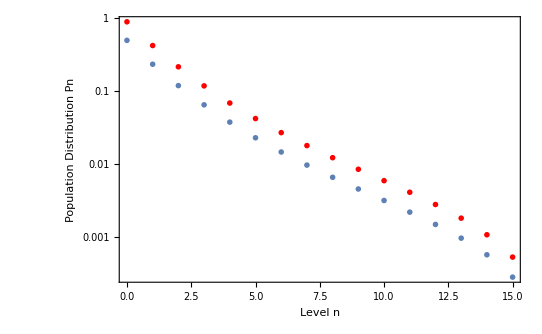

```mathematica
tel = 0.0001;
SteadyState = Table[
func = Pmen[[n+1]]/.First[sol];
steadyvalue = func[tel];
{n, steadyvalue},{n,0,15}]
(*ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"}]*)
SteadySum = Sum[func  = Pmen[[n+1]]/.First[sol];
func[tel], {n,0, nmax}];
NormalizedSteadyState =Table[{n,SteadyState[[n+1]][[2]] / SteadySum },{n,0,15}] ;
p1 =ListLogPlot[NormalizedSteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True,PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"},FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}];
p2 = ListLogPlot[Table[{n,Eigenvectors[R][[16]][[n+1]]},{n,0,nmax}], PlotMarkers -> {Automatic,Small}, PlotStyle -> Red, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"},FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}];
Show[{p1,p2}, PlotRange -> All]
```

## 5. Calculate Temperature

```mathematica
(*Bose Einstein critic. Temp*)
Nsite = 1 (*1 atom per lkattice site*)
Tc = 0.94 hbar ω0 /kb * Nsite^(1/3)
```

1

9.33385×10^-6

```mathematica
from Simulation
```

```mathematica
GroundStateFraction = NormalizedSteadyState[[0+1]][[2]];
Tmin = (1- GroundStateFraction)^(1/3)*Tc *10^6 (*μK*)
```

7.47259

```mathematica
from R Eigenvector
```

```mathematica
GroundStateFraction = Eigenvectors[R][[16]][[0+1]];
Tmin = (1- GroundStateFraction)^(1/3)*Tc *10^6 (*μK*)
```

4.68308+0. ⅈ